3/10 x^2 Cos[x^3/10]

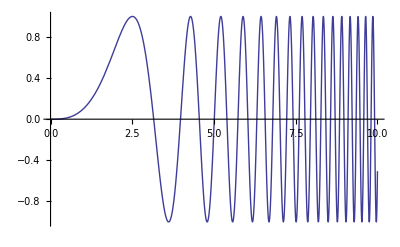

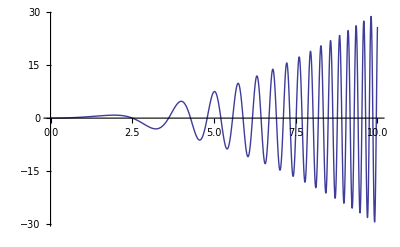

```mathematica
f[x_]:=Sin[x^3/10];
ff[x_]=D[f[x],x]
Plot[f[x],{x,0,10}]
Plot [ff[x],{x,0,10}]
```

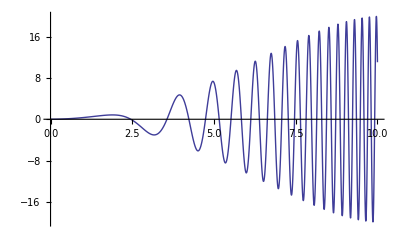

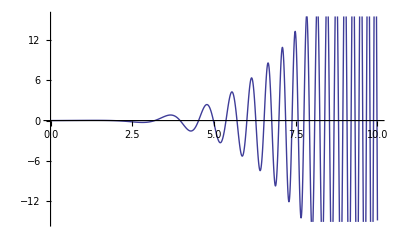

```mathematica
(* metoda liniowa *)
h=0.1;
ff1[x0_]=(f[x0+h]-f[x0])/h;
Plot[ff1[x],{x,0,10}]
Plot[ff1[x]-ff[x],{x,0,10}]
```

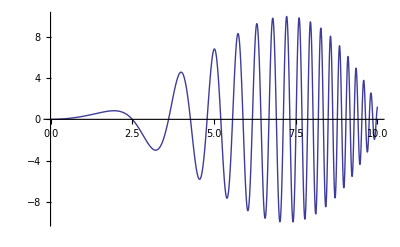

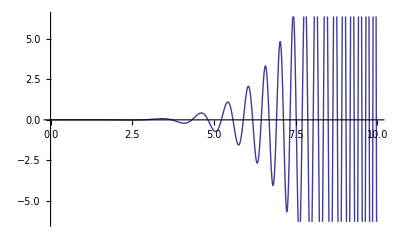

```mathematica
(* metoda szeregu II stopnia *)
h=0.1;
ff2[x0_]=(f[x0+h]-f[x0-h])/(2h);
Plot[ff2[x],{x,0,10}]
Plot[ff2[x]-ff[x],{x,0,10}]
```

```mathematica
(* Metoda mniejszych kwadratów *)
```

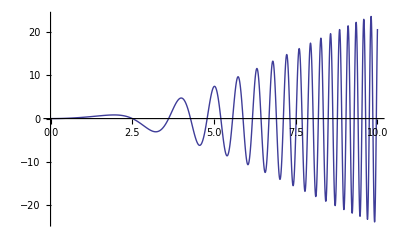

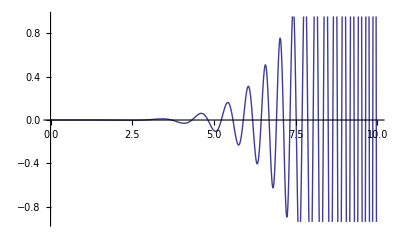

```mathematica
h=0.01;n=10;
ffnk[x_]=(Sum[(f[x+(i-n/2) h]-f[x]) (i-n/2) h,{i,1,n}] Sum[((i-n/2) h)^4,{i,1,n}]-Sum[(f[x+(i-n/2) h]-f[x]) ((i-n/2) h)^2,{i,1,n}] Sum[((i-n/2) h)^3,{i,1,n}])/(Sum[((i-n/2) h)^2,{i,1,n}] Sum[((i-n/2) h)^4,{i,1,n}]-Sum[((i-n/2) h)^3,{i,1,n}] Sum[((i-n/2) h)^3,{i,1,n}]);
Plot[ffnk[x],{x,0,10}]
Plot[ffnk[x]-ff[x],{x,0,10}]
```

```mathematica
(* Metoda oparta na interpolacji wielomianowej *)
```